### Define the transfer function engine thrust and throttle position

Transfer Function force exerted by engines on the aircraft due to the throttle position

```mathematica
Ge[s_]=500000/(s+2);
```

Unit Step  Input response, Transfer Function will allow the output function

```mathematica
U[s_]= 1/s;
Fe[s_]= Ge[s]*U[s]
```

500000/(s (2+s))

```mathematica
y[t_]= InverseLaplaceTransform[Fe[s],s,t]
```

500000 (1/2-ⅇ^(-2 t)/2)

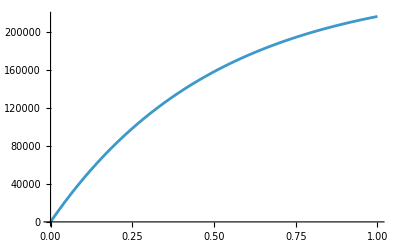

```mathematica
Plot[y[t],{t,0,1},
PlotRange->All]
```

### The relationship b/w the catapult force and the commanded catapult force is given by the

```mathematica
Gc[s_]= 5200000/(s^2+4 s+13);
Uc[s_]= 1/s;
```

```mathematica
Fc[s_]= Gc[s]*Uc[s]
```

5200000/(s (13+4 s+s^2))

```mathematica
fc[t_]= InverseLaplaceTransform[Fc[s],s,t]
```

200000/3 (6-(3+2 ⅈ) ⅇ^((-2-3 ⅈ) t)-(3-2 ⅈ) ⅇ^((-2+3 ⅈ) t))

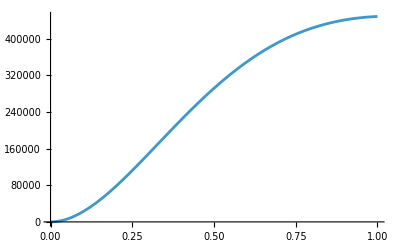

```mathematica
Plot[fc[t],{t,0,1},
PlotRange->All]
```

### Defining the Position and Velocity of aircraft in response to input force

G_p(s) = (X(s))/(U(s))
G_v(s) = (V(s))/(U(s))
mx^(..)(t) = u(t)-f_d(t)    where  f_d is the drag force = cẋ(t) (c is 100 N s/m)
Taking the Laplace Transform of the equation (negtecting the ICs due to T.F)


X(s) =(U(s))/(ms^2+cs) and position transfer function is
                                      G_p(s) = 1/(ms^2+cs)

For velocity ;
s*  G_p(s) =G_v(s)  and the velocity transfer function
                                     G_v(s) =1/(ms+c)